Bretcher 2.2.4 Linear Transformations

```mathematica
MatrixForm[tm={{1, 1}, {-1, 1}}];
x={0,1};
```

Setting up the tranformation matrix tm and the starting vector x.

```mathematica
n=8;
v = Table[0,{n}];
v[[0]]=x;
For[i=1,i≤n,i++,v[[i]]= tm.v[[i-1]]];
```

n as in n elements, v as the array filled with our transformations, v[0] as the first element (x)-

A for loop to iterate through the list and perform an additional transformation on every step in the  array.

```mathematica
v
```

{0,1}[{1,1},{2,0},{2,-2},{0,-4},{-4,-4},{-8,0},{-8,8},{0,16}]

Elements lies in the array v and is ready to be presented in a graph. We then use graphics - Arrow to represent and compared the different vectors although a vector doesn’t have a position.

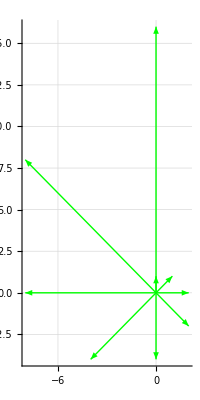

```mathematica
Graphics[{Green,Arrow[{origin,v[[0]]}],Green,Arrow[{origin,v[[1]]}],Green,Arrow[{origin,v[[2]]}],Green,Arrow[{origin,v[[3]]}],Green,Arrow[{origin,v[[4]]}],Green,Arrow[{origin,v[[5]]}],Green,Arrow[{origin,v[[6]]}],Green,Arrow[{origin,v[[7]]}],Green,Arrow[{origin,v[[8]]}]},Axes->True,GridLines->Automatic]
```

The Transformation scales and rotates the vector clockwise 45 degrees.